```mathematica
ClearAll["Global`*"]

fun1=x'[t]== mu*x[t]-y[t]+x[t]*(x[t]^2+y[t]^2)-x[t]*(x[t]^2+y[t]^2)^2+Cs;
fun2=y'[t]== x[t]+mu*y[t]+y[t]*(x[t]^2+y[t]^2)-y[t]*(x[t]^2+y[t]^2)^2+Cs;
x'[t]=D[r[t]*Cos[θ[t]],t];
y'[t]=D[r[t]*Sin[θ[t]],t];
x[t]=r[t]*Cos[θ[t]];
y[t]=r[t]*Sin[θ[t]];

chv=Solve[{fun1,fun2},{r'[t],θ'[t]}];
```

```mathematica
funr=r'[t]== -((-Cs Cos[θ[t]]-mu Cos[θ[t]]^2 r[t]-Cos[θ[t]]^4 r[t]^3+Cos[θ[t]]^6 r[t]^5-Cs Sin[θ[t]]-mu r[t] Sin[θ[t]]^2-2 Cos[θ[t]]^2 r[t]^3 Sin[θ[t]]^2+3 Cos[θ[t]]^4 r[t]^5 Sin[θ[t]]^2-r[t]^3 Sin[θ[t]]^4+3 Cos[θ[t]]^2 r[t]^5 Sin[θ[t]]^4+r[t]^5 Sin[θ[t]]^6)/(Cos[θ[t]]^2+Sin[θ[t]]^2));
funθ=θ'[t]==-1/(r[t] (1+Tan[θ[t]]^2))Cos[θ[t]]^4 (-r[t] Sec[θ[t]]^4-Cs Sec[θ[t]]^5+Cs Sec[θ[t]]^5 Tan[θ[t]]-r[t] Sec[θ[t]]^4 Tan[θ[t]]^2);
```

```mathematica
funa=-((-Cs Cos[θ[t]]-mu Cos[θ[t]]^2 r[t]-Cos[θ[t]]^4 r[t]^3+Cos[θ[t]]^6 r[t]^5-Cs Sin[θ[t]]-mu r[t] Sin[θ[t]]^2-2 Cos[θ[t]]^2 r[t]^3 Sin[θ[t]]^2+3 Cos[θ[t]]^4 r[t]^5 Sin[θ[t]]^2-r[t]^3 Sin[θ[t]]^4+3 Cos[θ[t]]^2 r[t]^5 Sin[θ[t]]^4+r[t]^5 Sin[θ[t]]^6)/(Cos[θ[t]]^2+Sin[θ[t]]^2));
funb=-1/(r[t] (1+Tan[θ[t]]^2))Cos[θ[t]]^4 (-r[t] Sec[θ[t]]^4-Cs Sec[θ[t]]^5+Cs Sec[θ[t]]^5 Tan[θ[t]]-r[t] Sec[θ[t]]^4 Tan[θ[t]]^2);
fp1=Solve[{funa== 0,funb==0},{r[t],θ[t]}];
```

```mathematica
r0=r[t]/.fp1;
θ0=θ[t]/.fp1;
```

```mathematica
J={{D[funa,r[t]],D[funa,θ[t]]},{D[funb,r[t]],D[funb,θ[t]]}};
trj=Tr[J];
detj=Det[J];
trj0=trj/.r[t]->r0/.θ[t]-> θ0;
detj0=detj/.r[t]->r0/.θ[t]-> θ0;
```

```mathematica
funb0=funb/.r[t]->r0/.θ[t]->θ1;
```

```mathematica
Tper = Integrate[1/funb0,{θ1,0,2*Pi}]
```

```mathematica
Tper={(2 π √Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,1] √(((Cs+√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,1])^2)/(-2 Cs^2+Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,1])))/(Cs+√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,1]),-((2 π √Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,1] √(((Cs-√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,1])^2)/(-2 Cs^2+Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,1])))/(Cs-√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,1])),(2 π √Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,2] √(((Cs+√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,2])^2)/(-2 Cs^2+Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,2])))/(Cs+√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,2]),-((2 π √Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,2] √(((Cs-√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,2])^2)/(-2 Cs^2+Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,2])))/(Cs-√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,2])),(2 π √Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,3] √(((Cs+√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,3])^2)/(-2 Cs^2+Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,3])))/(Cs+√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,3]),-((2 π √Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,3] √(((Cs-√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,3])^2)/(-2 Cs^2+Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,3])))/(Cs-√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,3])),(2 π √Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,4] √(((Cs+√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,4])^2)/(-2 Cs^2+Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,4])))/(Cs+√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,4]),-((2 π √Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,4] √(((Cs-√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,4])^2)/(-2 Cs^2+Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,4])))/(Cs-√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,4])),(2 π √Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,5] √(((Cs+√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,5])^2)/(-2 Cs^2+Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,5])))/(Cs+√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,5]),-((2 π √Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,5] √(((Cs-√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,5])^2)/(-2 Cs^2+Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,5])))/(Cs-√Root[-2 Cs^2+(1+mu^2) #1+2 mu #1^2+(1-2 mu) #1^3-2 #1^4+#1^5&,5]))};
```

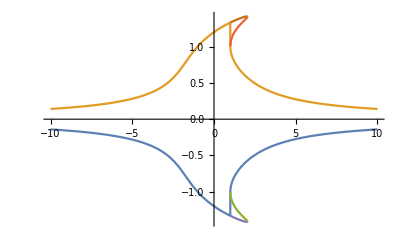

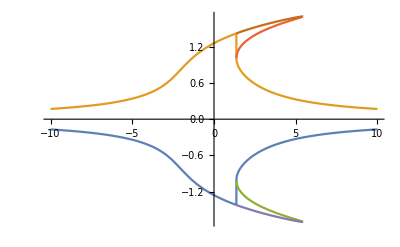

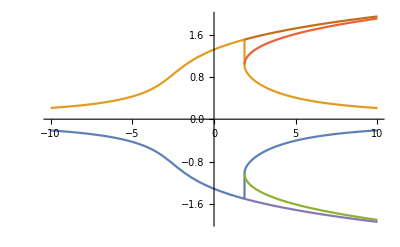

```mathematica
Cs=1;
Plot[r0,{mu,-10,10}]
Cs=1.2;
Plot[r0,{mu,-10,10}]
Cs=1.5;
Plot[r0,{mu,-10,10}]
Clear[Cs]
```

```mathematica
fprr=Solve[r0[[3]]==r0[[5]],mu]
```

Solve::useq: The answer found by Solve contains equational condition(s) {0 == Root[-2\ Power[« 2 »] + Plus[« 2 »]\ Slot[« 1 »] + 2\ mu\ Power[« 2 »] + Plus[« 2 »]\ Power[« 2 »] - 2\ Power[« 2 »] + Slot[« 1 »]^5 &, 2] - Root[Times[« 2 »] + Times[« 2 »] + Times[« 3 »] + Times[« 2 »] + Times[« 2 »] + Power[« 2 »] &, 3], 0 == √Root[Times[« 2 »] + Times[« 2 »] + Times[« 3 »] + Times[« 2 »] + Times[« 2 »] + Power[« 2 »] &, 2] - √Root[Plus[« 6 »] &, 3]}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}